```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
a=1
```

1

```mathematica
b=5
```

5

```mathematica
f[x_]:=a*x^2
```

```mathematica
f2[x_]:=b*x^2
```

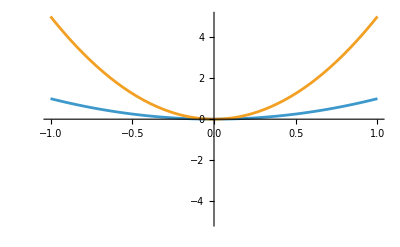

```mathematica
Plot[{f[x],f2[x]},{x,-1,1},PlotRange->5]
```

```mathematica
(* let a be a animation variable *)
```

```mathematica
f1[x_,a_]:=a*x^2
```

```mathematica
Animate[Plot[f1[x,a],{x,-1,1},PlotRange->5],{a,1,5,1}]
```

```mathematica
Manipulate[Plot[f1[x,a],{x,-1,1},PlotRange->5],{a,1,5,1}]
```

```mathematica
p={1,3,-5}
```

{1,3,-5}

```mathematica
Point1={Red,PointSize[0.05],Point[p]}
```

{RGBColor[1, 0, 0],PointSize[0.05],Point[{1,3,-5}]}

```mathematica
Graphics3D[Point1,Axes->True,BoxRatios->1,AxesOrigin->{0,0,0},Boxed->False,PlotRange->6]
```

-Graphics3D-